## Initialisation

```mathematica
mLi6=Quantity[9.9883414*^-27,"Kilogram"];
mEr168=Quantity[167.93237*1.660539*^-27,"Kilogram"];
hbar=Quantity["ReducedPlanckConstant"];
h=Quantity["PlanckConstant"];
kb = Quantity["BoltzmannConstant"];
c = Quantity["SpeedOfLight"];
mub = Quantity["BohrMagneton"];
calcFermiE[n_,m_]:= hbar^2/(2*m)*(3*Pi^2*n)^(2/3)
calcFermiT[n_,m_]:=UnitSimplify[calcFermiE[n,m]/kb]
calcRecoilE[m_,wvl_]:=UnitSimplify[h^2/(2*m*wvl^2)]
calcRecoilF[m_,wvl_]:=UnitConvert[calcRecoilE[m,wvl]/h,"Hertz"]
calcRecoilT[m_,wvl_]:=UnitSimplify[calcRecoilE[m,wvl]/kb]
```

## Fermi energy

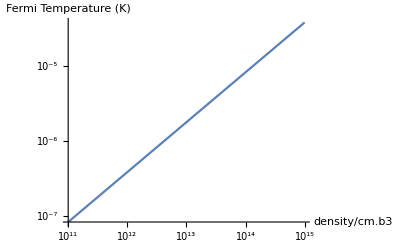

```mathematica
Ef = calcFermiE[Quantity[10*^15,"Centimeter^-3"],mLi6];
Ef = UnitSimplify[Ef];
Tf =calcFermiT[Quantity[10*^15,"Centimeter^-3"],mLi6];
LogLogPlot[{calcFermiT[Quantity[x,"Centimeter^-3"],mLi6]},{x,10^11,10^15},AxesLabel->{"density/cm.b3","Fermi Temperature (K)"}]
```

## Recoil energy

```mathematica
D1wvl =Quantity[670.992421,"nanometer"] (*vacuum*)
D2wvl =Quantity[670.977338,"nanometer"](*vacuum*)
D1gamma = Quantity[5.8724,"megahertz"]
D2gamma= D1gamma
Er1064=calcRecoilE[mLi6,Quantity[1064,"Nanometers"]];
Tempr1064 = calcRecoilT[mLi6,Quantity[1064,"Nanometers"]];
fr1064= calcRecoilF[mLi6,Quantity[1064,"Nanometers"]];
Er532=calcRecoilE[mLi6,Quantity[532,"Nanometers"]];
Tempr532 = calcRecoilT[mLi6,Quantity[532,"Nanometers"]];
fr532= calcRecoilF[mLi6,Quantity[532,"Nanometers"]];
```

670.992 nm

670.977 nm

5.8724 MHz

5.8724 MHz

## Tunnelling rate

The nearest-neighbour tunneling rate for deep lattices (V>15 E_r) is given by
t/E_r=4/(√π)(V_1/E_r)^(3/4)exp(-2 √(V_0/E_r))

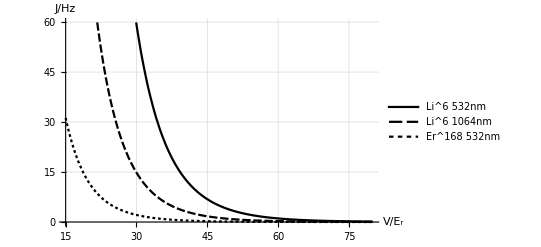

```mathematica
t[V_]:=4/Sqrt[Pi]*V^(3/4)*Exp[-2Sqrt[V]]
Plot[{UnitConvert[t[V]* fr532,"Hertz"],UnitConvert[t[V]* fr1064,"Hertz"],UnitConvert[t[V]*calcRecoilF[mEr168,Quantity[532,"Nanometer"]],"Hertz"]},{V,15,80},PlotTheme->"Monochrome",AxesLabel->{"V/\!\(\*SubscriptBox[\(E\), \(r\)]\)","J/Hz"},GridLines->Automatic,PlotLegends->{"Li^6 532nm","Li^6 1064nm","Er^168 532nm"}]
```

What lattice depth is required to reduce the tunnelling rate below 0.1Hz (in standing wave lattices with a=532nm and 256nm)?

```mathematica
Solve[t[V]* fr1064==Quantity[0.1,"Hertz"],V]
Solve[t[V]* fr532==Quantity[0.1,"Hertz"],V]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{V→1.73663×10^-8},{V→68.673}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{V→2.73444×10^-9},{V→81.8261}}

## Gravity v magnetic field gradient

What magnetic field gradient is required to overcome the gravitational pull? This is a useful quantity to remember.  
Zeeman regime 
In the Zeeman regime we have  H= -μ_B m_F g_F B. The Lande g-factor is defined as:

```mathematica
calcGf[i_,J_,F_,gI_,gJ_]=gJ(F(F+1)-i(i+1)+J(J+1))/(2F(F+1))+gI(F(F+1)+i(i+1)-J(J+1))/(2F(F+1));
```

```mathematica
For the ground state namifold we have
```

```mathematica
(*For the GS hyperfine manifold in Li6:*)
gf=calcGf[1,1/2,1/2,-0.0004476540,2.0023010]
```

-0.668031

Now we can find the slope of the energy per Gauss from δH/δB= -μ_B m_F g_F and the corresponding required magnetic field gradient to counter gravity from mg=g_J m_J μ_B dB/dz

```mathematica
slope = UnitConvert[mub/h*1/2*gf,"Megahertz/Gauss"]
gradient = UnitConvert[mLi6*Quantity[9.81,"Meter/Second^2"]/(h*slope),"Gauss / centimeter"]
```

-0.467496 MHz/G

-3.16321 G/cm

Paschen - Back regime
In the Paschen - Back regime the hyperfine coupling is lifted, so the Hamiltonian becomes H= (-μ_B m_J g_J -μ_B m_I g_I)B. The nuclear g-factor is smaller by four orders of magnitude so we can neglect it here. Moreover we know that g_J=2.0023010 for the ground state. Therefore

```mathematica
slope = UnitConvert[mub/h*1/2*gJ,"Megahertz/Gauss"]/.gJ->2.0023010
gradient = UnitConvert[mLi6*Quantity[9.81,"Meter/Second^2"]/(h*slope),"Gauss / centimeter"]
```

1.40123 MHz/G

1.05535 G/cm

## High-field splitting of m_I-states

In the Paschen-Back regime we recover two triplet manifolds for the two different electron spin states. The full hyperfine Hamiltonian in this regime is
H= -μ_B m_J g_J B+μ_K m_I g_I B-a_HF m_J m_I
where the a_HF=152.1368407MHz is the Hyperfine splitting of the Ground state manifold. Note that this is an approximation to first order in a_HF m_J m_I. Within the lower triplet g_J is the same and the nuclear part is small

```mathematica
a= Quantity[152.1368407,"Megahertz"];
splitting =a/2
```

76.0684 MHz

```mathematica
drift=UnitConvert[-0.0004476540mub/h,"Hertz/Gauss"]
```

-626.548 Hz/G

## Gaussian beam and dipole traps

The intensity profile of a Gaussian beam is given by
I(ρ,z)=(I_0(w_0/(w(z))))^2 exp(-2(ρ/(w(z)))^2)
with a peak intensity of I_0=(2P)/πw_0^2 and waist given by
w(z)=w_0 √(1+(z/z_R)^2).

```mathematica
zr[wvl_,w0_]:=Pi*w0^2/wvl
w[wvl_,w0_,z_]:=w0*Sqrt[1+(z/zr[wvl,w0])^2]
Int[P_,wvl_,w0_,r_,z_]:=2P/(Pi*w0^2)*E^(-2(r/w[wvl,w0,z])^2)
(*Numeric example for the peak intensity of a dipole trap*)
int=Int[0.1,1064*10^-9,25*10^-6,0,0]
```

1.01859×10^8

Let’s define the saturation intensity for the Li D-line

```mathematica
hb=1.054571817*10^-34;
D2Gamma=2Pi*5.9*10^6;
mLi6=9.9883414*10^-27;
kB=1.38*10^-23;
Isat[wvl_,gamma_]:=2Pi^2 *hb*2.998 *10^8 * D2Gamma/3/wvl^3;
IsatDLine=Isat[671*10^-9,D2Gamma];
Print["Saturation Intensity (W/m^2): ", IsatDLine]
```

Saturation Intensity (W/m^2): 25.5259

```mathematica
trapP = 100;
trapWvl = 1070*10^-9;
trapWaist = 25*10^-6;
Print["Power (W):",trapP]
Print["Wavlength (m):",N[trapWvl] ]
Print["Waist (um):",N[trapWaist*10^6]]

U0[Inten_,wvl_,gamma_]:=hb/(4*2*Pi*2.998*10^8*(1/671/10^-9-1/wvl))*D2Gamma^2/2*Inten/IsatDLine

Print["Trap depth U_0 (uK):",
U0[Int[trapP,trapWvl,trapWaist,0,0],trapWvl,D2Gamma]/kB*10^6]

(*Define Radial Trap frequency *)
TrapFreqRadial[P_,m_,w_]:=Sqrt[4*U0[Int[P,trapWvl,trapWaist,0,0],trapWvl,D2Gamma]/(m*w^2)]
Print["Radial trap frequency ω_r/2Π (Hz): ",TrapFreqRadial[trapP,mLi6,trapWaist]/(2Pi)]

(*Define Axial Trap frequency *)TrapFreqAxial[P_,m_,w_]:=Sqrt[2*U0[Int[P,trapWvl,trapWaist,0,0],trapWvl,D2Gamma]/(m*zr[trapWvl,w]^2)]
Print["Axial trap frequency ω_r/2Π (Hz): ",TrapFreqAxial[trapP,mLi6,trapWaist]/(2Pi)]
```

Power (W):100

Wavlength (m):1.07×10^-6

Waist (um):25.

Trap depth U_0 (uK):5003.94

Radial trap frequency ω_r/2Π (Hz): 33478.

Axial trap frequency ω_r/2Π (Hz): 322.506

## Diagonalisation

Define spin operators

```mathematica
SpinQ[S_] := IntegerQ[2*S] && S >= 0
splus[0] = {{0}} //SparseArray;
splus[S_?SpinQ] := splus[S] = SparseArray[Band[{1,2}] -> Table[Sqrt[S(S+1)-M(M+1)],{M,S-1,-S,-1}], {2S+1,2S+1}]
sminus[S_?SpinQ] := Transpose[splus[S]]
sx[S_?SpinQ] := sx[S] = (splus[S]+sminus[S])/2
sy[S_?SpinQ] := sy[S] = (splus[S]-sminus[S])/(2I)
sz[S_?SpinQ]:=sz[S]=SparseArray[Band[{1,1}]->Range[S,-S,-1],{2S+1,2S+1}]
id[S_?SpinQ] := id[S] = IdentityMatrix[2S+1, SparseArray]
```

Define spin operators for Lithium with I = 1, S=1/2, L=0:

```mathematica
Ix=KroneckerProduct[sx[1],id[1/2],id[0]];
Iy=KroneckerProduct[sy[1],id[1/2],id[0]];
Iz=KroneckerProduct[sz[1],id[1/2],id[0]];
Sx=KroneckerProduct[id[1],sx[1/2],id[0]];
Sy=KroneckerProduct[id[1],sy[1/2],id[0]];
Sz=KroneckerProduct[id[1],sz[1/2],id[0]];
Lx=KroneckerProduct[id[1],id[1/2],sx[0]];
Ly=KroneckerProduct[id[1],id[1/2],sy[0]];
Lz=KroneckerProduct[id[1],id[1/2],sz[0]];
```

```mathematica
Jx=Sx+Lx;
Jy=Sy+Ly;
Jz=Sz+Lz;
Fx=Ix+Jx;Fy=Iy+Jy;Fz=Iz+Jz;
Hhf=A(Ix.Jx+Iy.Jy+Iz.Jz)-ub*Bz*(gI*Iz+gS*Sz+gL*Lz);
```

```mathematica
(*values from Gehm (2003)*)
hfc={A->Quantity[152.1368407,"MHz"], ub-> Quantity["BohrMagneton"]/h*Quantity[1,"Gauss"],gS->2.0023193043737,gL->0.99999587,gI->+0.0004476540}
```

{A→152.137 MHz,ub→1 μ_B G/h,gS→2.00232,gL→0.999996,gI→0.000447654}

```mathematica
(*find eigenvalues and eigenvectors*)
(*caution: cell evaluation takes a while! *)
{eval, evec}=Eigensystem[Hhf]//FullSimplify;
```

Plot the Breit-Rabi diagram for the ground state

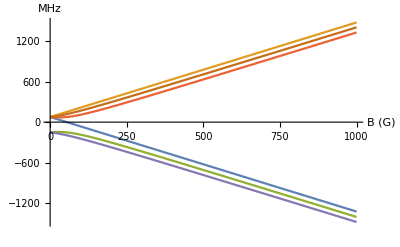

```mathematica
Plot[Evaluate[eval/.hfc],{Bz,0,1000},AxesLabel->{"B (G) ","MHz"}]
```

Find the splitting between any two levels at any magnetic field

```mathematica
eigs= Evaluate[eval/.Join[hfc,{Bz->800}]];
eigs = Sort[eigs]
eigs[[1]]-eigs[[2]]
eigs[[2]]-eigs[[3]]
eigs[[3]]-eigs[[4]]
eigs[[4]]-eigs[[5]]
eigs[[5]]-eigs[[6]]

eigs[[2]]-eigs[[5]]
```

{-1201.55 MHz,-1126.33 MHz,-1045.43 MHz,1049.76 MHz,1125.98 MHz,1197.57 MHz}

-75.2188 MHz

-80.8984 MHz

-2095.19 MHz

-76.2212 MHz

-71.5868 MHz

-2252.31 MHz

```mathematica
Evaluate[evec/.Join[hfc,{Bz->600}]]//FullSimplify
```

{{1,0,0,0,0,0},{0,0,0,0,0,1},{0,-0.0667256,1,0,0,0},{0,14.9868,1,0,0,0},{0,0,0,-0.0609933,1,0},{0,0,0,16.3952,1,0}}

```mathematica
eigs=Assuming[A>0 &&ub>0 &&Bz>0&&0<gI<gL<gS, Sort[eval/.Join[hfc,{Bz->800}]]]
```

{-1201.55 MHz,-1126.33 MHz,-1045.43 MHz,1049.76 MHz,1125.98 MHz,1197.57 MHz}

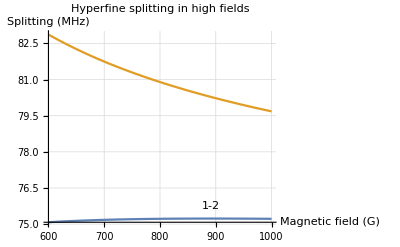

```mathematica
lists={eval/.Join[hfc,{Bz->800}],eval/.hfc};
listsSort=SortBy[listsᵀ,First]ᵀ;
eigsSort=listsSort[[2]];
Plot[{eigsSort[[2]]-eigsSort[[1]],eigsSort[[3]]-eigsSort[[2]]},{Bz,600,1000},PlotLabels->Placed[{"1-2","2-3"},{Above}], PlotLabel->"Hyperfine splitting in high fields", AxesLabel->{"Magnetic field (G)","Splitting (MHz)"},GridLines->Automatic]
```

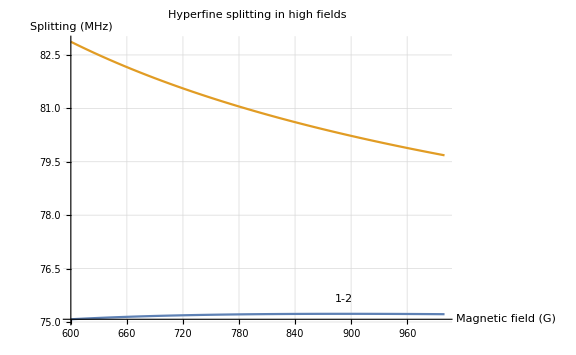

```mathematica
Show[%141,ImageSize->Large]
```

```mathematica
Export["D:\\rzgdatashare\\FermiQP-Team\\users\\robin\\calculations\\RF_splitting_highFields.jpg",%151,"JPEG"]
```

D:\rzgdatashare\FermiQP-Team\users\robin\calculations\RF_splitting_highFields.jpg

```mathematica
Export["D:\\rzgdatashare\\FermiQP-Team\\users\\robin\\calculations\\RF_splitting_highFields.jpg",%141,"JPEG"]
```

D:\rzgdatashare\FermiQP-Team\users\robin\calculations\RF_splitting_highFields.jpg

```mathematica
eigsSort=eval/.hfc;
forSorting=Evaluate[eval/.hfc,Bz->800];
eigsSort=eigsSort[[Ordering @ forSorting]];
Plot[{eigsSort[[2]]-eigsSort[[1]]},{Bz,600,800}]
```

Ordering::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Ordering[{1/2 (Bz Quantity[-2.00321,BohrMagneton Gauss Power[«2»]]+152.137),«4»,1/4 (-+Bz Quantity[0.000895308,BohrMagneton …s Power[«2»]]+√(Power[«2»] Quantity[«2»]+Bz Quantity[«2»]+Quantity[208311.,Power[«2»]]))},Bz→«3»].

Part::pkspec1: The expression Ordering[{1/2 (Bz Quantity[-2.00321,BohrMagneton Gauss Power[«2»]]+152.137),«4»,1/4 (-+Bz Quantity[0.000895308,BohrMagneton …s Power[«2»]]+√(Power[«2»] Quantity[«2»]+Bz Quantity[«2»]+Quantity[208311.,Power[«2»]]))},Bz→«3»] cannot be used as a part specification.

Ordering::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Ordering[{-,917.199,-,771.488,-,847.316},600.004→800].

Part::pkspec1: The expression Ordering[{-,917.199,-,771.488,-,847.316},600.004→800] cannot be used as a part specification.

Ordering::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Ordering[{-,917.199,-,771.488,-,847.316},600.004→800].

Part::pkspec1: The expression Ordering[{-,917.199,-,771.488,-,847.316},600.004→800] cannot be used as a part specification.

Ordering::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Ordering[{-,917.199,-,771.488,-,847.316},600.004→800.].

General::stop: Further output of Ordering::seqs will be suppressed during this calculation.

Part::pkspec1: The expression Ordering[{-,922.921,-,777.154,-,852.993},604.086→800] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-Graphics-